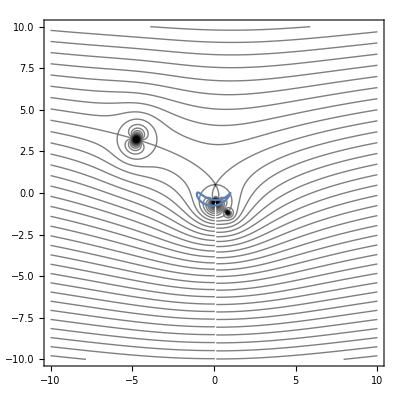
-Graphics-g=2

```mathematica
Options[fieldPlot]={"size"->10, Contours->40,"FieldLines"->80,"FieldLineStyle"->Directive[Black,Thick],"PotentialStyle"->{Directive[Thick,Darker[Cyan]]},ExclusionsStyle->None,Exclusions->None};

fieldPlot[g_,f_,opts:OptionsPattern[]]:=Module[{im,re,xM,yM},xM=OptionValue["size"]; yM=xM;
R=1;
disk= Graphics[{Darker[Blue,0.8],Disk[{0,0},{R,R}]}];
p2=ParametricPlot[{Re[f[R*Exp[I* phi]+z0]], Im[f[R*Exp[I* phi]+z0]]},{phi,0,2*Pi},PlotRange->3];
im=ContourPlot[Im[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,ContourStyle->OptionValue["FieldLineStyle"],Contours->OptionValue["FieldLines"],PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->2];
re=ContourPlot[Re[g[x+I y]],{x,-xM,xM},{y,-yM,yM},ContourShading->False,FrameLabel->{"Re(z)","Im(z)"},ContourStyle->OptionValue["PotentialStyle"],Contours->OptionValue[Contours],Exclusions->OptionValue[Exclusions],
ExclusionsStyle->OptionValue[ExclusionsStyle]];
Show[im,p2,Background->White,Frame->True,AspectRatio->Automatic]]
Clear[arg,log];
R=1; G=2;
size= 10;
arg[z_,σ_:-Pi]:=Arg[z Exp[-I (σ+Pi)]]+σ+Pi;
log[z_,σ_:-Pi/2]:=Log[Abs[z]]+I arg[z,σ];
f[z_]:=1/2*(z+1/z);
z0 =0.095-0.5*I;
g[z_] := f[z-z0+R^2/(z-z0)+log[z-z0]/I*G];
s=Labeled[fieldPlot[g,f,"size"->size],"g="~~ToString[G]~~""]
SetDirectory[NotebookDirectory[]];
Export["plot"~~ToString[G]~~".pdf",s,"PDF","AllowRasterization"->False];
```

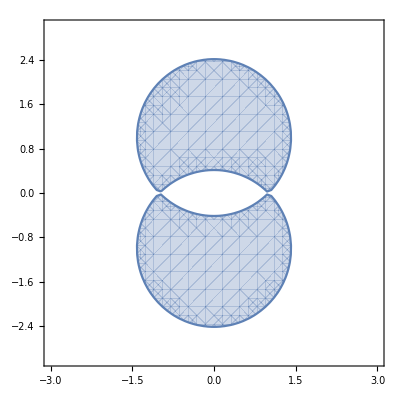

```mathematica
RegionPlot[Abs[f[x+I y]]<1,{x,-3,3},{y,-3,3}]
```

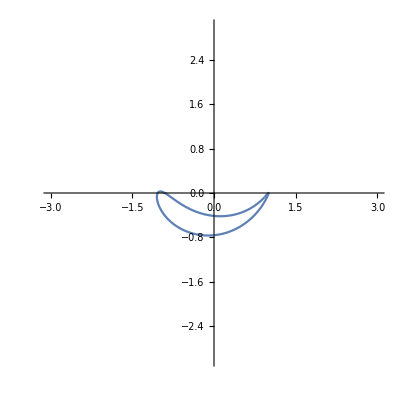

```mathematica
z0 =0.095-0.5*I;
p1=ParametricPlot[{Re[R*Exp[I* phi]+z0], Im[R*Exp[I* phi]+z0]},{phi,0,2*Pi},PlotRange->3];
p2=ParametricPlot[{Re[f[R*Exp[I* phi]+z0]], Im[f[R*Exp[I* phi]+z0]]},{phi,0,2*Pi},PlotRange->3];
Show[p2]
```